```mathematica
(*INIITIALIZE PARAMETERS*)

alpha = 0.5;
beta = 1.0;
delta = 0.5;
katta =5;
qAvg = 1.0;
eta = 0.25;
etaBar = 0.5;
chi = 0.1;
uBar = 1.0;
R=20;
T = 100;

(*AGENTS*)

(*Number of firms*)
n = 10.0;

(*Number of consumers*)
m= 100.0;
```

```mathematica
(*PRICING*)

(*market share of the specialized firm*)
ms[q0_, qi_]:= q0 / Total[qi];

(*markup smart components*)
etaSpec[delta_, etaSpecLag_, q0_, qi_, etaBar_]:=(1-delta)*etaSpecLag + delta*ms[q0,qi]*etaBar;

(*price of specialist*)
pSpec[cs_,etaSpec_]:=(1+etaSpec)*cs;

(*price charged by the firm*)
pFirm[c_,eta_]:=(1+eta)*c;

(*price of firm if it produces the smart component*)
pFirmSelf[cSelf_,eta_]:=(1+eta)*cSelf;

(*price of firm if it produces the smart component*)
pFirmSpec[cSpec_,eta_]:=(1+eta)*cSpec;
```

```mathematica
(*MARGINAL COSTS*)

(*Marginal costs of the "usual" component*)
cp = 20.0;

(*Marginal costs of the smart component*)
cs = 10.0;

(*Marginal costs if firm buys smart component from specialist*)
cSelf[cp_, cs_]:=cp + cs;

(*Marginal cost if firm buys smart component from specialist*)
cSpec[cp_,cs_, etaSpec_]:=cp + (1+etaSpec)*cs;
```

```mathematica
(*PROFIT*)
profit[q_,p_,c_]:=q*p - c*q;
```

```mathematica
(*QUALITY*)

(*quality of specialist*)
qualitySpec[uBar_, alpha_, beta_,qSpec_ ] :=uBar*(1+ beta*qSpec^alpha);

(*quality of firm*)
qualityFirm[uBar_, alpha_, beta_,qFirm_ ] :=uBar*(1+ beta*qFirm^alpha);
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*--------------------------------------------------EXERCISE 1-----------------------------------------------------------------*)
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*A: FIXED STRATEGIES: FIRMS PRODUCE SMART COMPONENT*)
```

```mathematica
(*Vector of prices*)
priceList ={};
Do[AppendTo[priceList,pFirm[cSelf[cp,cs],eta]],{i,1,n}]
priceList
```

{37.5,37.5,37.5,37.5,37.5,37.5,37.5,37.5,37.5,37.5}

```mathematica
(*Vector of quantities - should be zero in initial time period*)
qFirm={};
Do[AppendTo[qFirm,0.0],{i,1,n}]
qFirm
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(*Vector of profits - depend on quantities, prices, and marginal cost*)
profitList ={};
Do[AppendTo[profitList,profit[qFirm[[i]],priceList[[i]],cSelf[cp,cs]]],{i,1,n}]
profitList
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(*Vector of qualities - depend on quantities*)
qualityList = {};
Do[AppendTo[qualityList,qualityFirm[uBar, alpha, beta,qFirm[[i]]]],{i,1,n}] 
qualityList
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
(*Vector of probabilities - depend on qualities and prices*)
probListAll ={};
Do[
(*Initialize a list of probabilities for each consumer*)
probList = {};
Do[
(*Compute probablility that consumer j buys form Firm i*)
prob= Exp[-chi*priceList[[i]]+ katta*qualityList[[i]]]/Sum[Exp[-chi*priceList[[k]]+ katta*qualityList[[k]]],{k,1,n}];
(*Append this probability to the list of probabilities for the j-th consumer*)
AppendTo[probList,prob],
{i,1,n}
];
(*Append this list to the list of probabilities of all Consumers*)
AppendTo[probListAll,probList],
{j,1,m}
]
```

```mathematica
(*The list of probabilities of the first consumer*)
probListAll[[1]]
```

{0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1}

```mathematica
(*The probability that the first consumer buys from firm 1*)
probListAll[[1,1]]
```

0.1

```mathematica
(*Sum of probabilitis should be equal to one*)
Total[probListAll[[1]]]
```

1.

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*QUESTION: Probabilities are equal so how to decide from which firm consumers should buy ?*)
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
probListAll;
```

```mathematica
(* Idea: Consumers decide randomly (iid) and their choice is a draw from a uniform distribution on S={s|s in 1,..,n} *)
```

```mathematica
(*A dummy vector to identify each firm by a number*)
Id = {};
Do[AppendTo[Id, i],{i,1,n}]
choiceList =RandomChoice[Id,m];
Do[qFirm[[i]] = Count[choiceList,i],{i,1,n}]
(*New quantities*)
qFirm
```

{9,9,7,9,11,11,15,11,8,10}

```mathematica
(*Vector of profits - depend on NEW quantities, prices, and marginal cost*)
profitList ={};
Do[AppendTo[profitList,profit[qFirm[[i]],priceList[[i]],cSelf[cp,cs]]],{i,1,n}]
profitList
```

{67.5,67.5,52.5,67.5,82.5,82.5,112.5,82.5,60.,75.}

```mathematica
(*Vector of NEW qualities - depend on NEW quantities*)
qualityList = {};
Do[AppendTo[qualityList,qualityFirm[uBar, alpha, beta,qFirm[[i]]]],{i,1,n}] 
qualityList
```

{4.,4.,3.64575,4.,4.31662,4.31662,4.87298,4.31662,3.82843,4.16228}

```mathematica
(*Vector of probabilities - depend on NEW qualities and prices*)
probListAll ={};
Do[
(*Initialize a list of probabilities for each consumer*)
probList = {};
Do[
(*Compute numerator*)
num= Exp[-chi*priceList[[i]]+ katta*qualityList[[i]]];
(*Compute denominator*)
denom ={};
Do[AppendTo[denom,Exp[-chi*priceList[[k]]+ katta*qualityList[[k]]]],
{k,1,n}];
(*Compute probablility that consumer j buys form Firm i*)
prob= num/(Total[denom]);
(*Append this probability to the list of probabilities for the j-th consumer*)
AppendTo[probList,prob]
,{i,1,n}];
(*Append this list to the list of probabilities of all Consumers*)
AppendTo[probListAll,probList],
{j,1,m}]
```

```mathematica
Position[probListAll[[1]],Max[probListAll[[1]]]]
```

{{7}}

```mathematica
probListAll[[1,7]]
```

0.793583

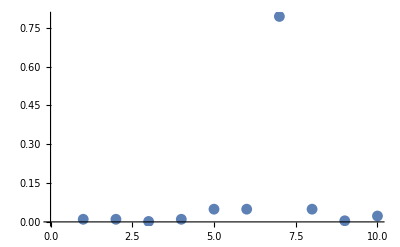

```mathematica
ListPlot[probListAll[[1]],PlotRange->All]
```